```mathematica
(*Define Behaviors:Human uploads less per day(2),Spammers upload more per day(50)*)
human=PoissonDistribution[2];
bot=PoissonDistribution[50];
```

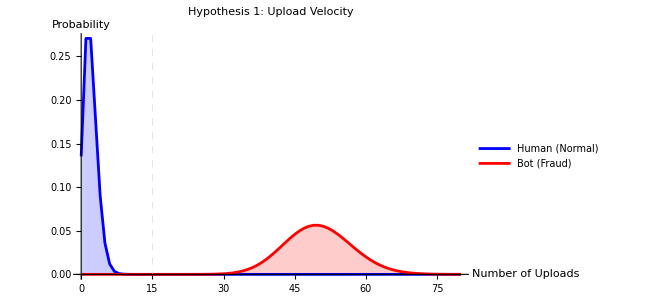

```mathematica
(*Hypothesis 1:Upload Velocity*)
DiscretePlot[{PDF[human,x],PDF[bot,x]},{x,0,80},Joined->True,PlotRange->All,PlotStyle->{Blue,Red},PlotLegends->{"Human (Normal)","Bot (Fraud)"},Filling->Axis,GridLines->{{15},None},GridLinesStyle->Dashed,PlotLabel->"Hypothesis 1: Upload Velocity",AxesLabel->{"Number of Uploads","Probability"}]
```

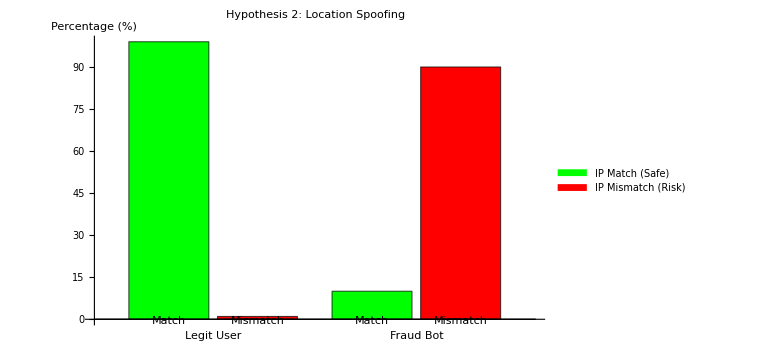

```mathematica
(*Hypothesis 2:Geolocation Mismatch*)BarChart[{{99,1},{10,90}},ChartLayout->"Grouped",ChartLabels->{{"Legit User","Fraud Bot"},{"Match","Mismatch"}},ChartStyle->{Green,Red},ChartLegends->{"IP Match (Safe)","IP Mismatch (Risk)"},PlotLabel->"Hypothesis 2: Location Spoofing",AxesLabel->{None,"Percentage (%)"},ImageSize->Large]
```

```mathematica
(*Define Behaviors:Human scores low (20),Spammers score high (85)*)
humanScore=NormalDistribution[20,15]; 
spamScore=NormalDistribution[85,5];
```

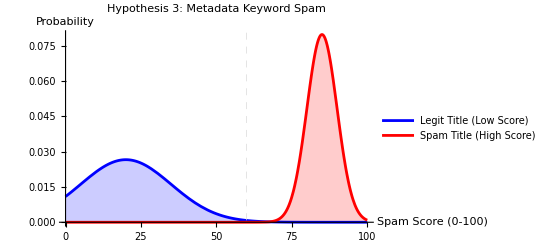

```mathematica
Plot[{PDF[humanScore,x],PDF[spamScore,x]},{x,0,100},PlotRange->All,PlotStyle->{Blue,Red},PlotLegends->{"Legit Title (Low Score)","Spam Title (High Score)"},Filling->Axis,GridLines->{{60},None},GridLinesStyle->Dashed,PlotLabel->"Hypothesis 3: Metadata Keyword Spam",AxesLabel->{"Spam Score (0-100)","Probability"}]
```